{Binding Energy cs, bs, cc, bc, bb}

-0.024638

-0.0319309

-0.0771545

-0.10134

-0.127854

{Ωc 1/2+ 2.695}

{2.67992,4.93209,{3.07937,2.95563,2.48388,2.04279}}

{0.280116}

{{-0.405781},{-0.384352},{-1.07344}}

{Ωc^* 3/2+ 2.766}

{2.76399,5.09818,{3.08138,2.96124,2.4935,2.04279}}

{0.288748}

{{-0.339317},{-0.321398},{-0.897615}}

{Ds 0- 1.968}

{1.96079,3.77218,{3.06052,2.90464,2.40961,2.04279}}

{0.460247,0.460247}

{Ds^* 1- 2.112}

{2.112,4.17185,{3.06817,2.92497,2.4367,2.04279}}

{0.505218,0.505218}

{{0.409368,-0.409368},{0.387749,-0.387749},{1.08292,-1.08292}}

{Ωb 1/2+ 6.046}

{6.07977,4.76782,{3.07725,2.94974,2.47414,2.04279}}

{0.595289}

{{-0.324031},{-0.306919},{-0.857179}}

{Ωb^* 3/2+}

{6.11184,4.84453,{3.07826,2.95253,2.47872,2.04279}}

{0.604289}

{{-0.540608},{-0.512059},{-1.4301}}

{Bs 0- 5.367}

{5.34623,3.35136,{3.05053,2.87893,2.37922,2.04279}}

{0.15794,0.15794}

{Bs^* 1- 5.415}

{5.415,3.61907,{3.05715,2.89586,2.39879,2.04279}}

{0.169303,0.169303}

{{0.380126,-0.380126},{0.360052,-0.360052},{1.00557,-1.00557}}

{ηc 0- 2.984}

{3.00152,3.15149,{3.04489,2.86478,2.36406,2.04279}}

{0.}

{Jψ 1- 3.097}

{3.097,3.54086,{3.05531,2.89113,2.39316,2.04279}}

{0.}

{{0.},{0.},{0.}}

{Bc 0- 6.275}

{6.27341,2.53047,{3.02189,2.81018,2.31371,2.04279}}

{0.294269,0.294269}

{Bc^* 1-}

{6.332,2.81377,{3.03359,2.83736,2.33731,2.04279}}

{0.324359,0.324359}

{{0.197958,-0.197958},{0.187504,-0.187504},{0.52367,-0.52367}}

{ηb 0- 9.399}

{9.39622,1.59034,{2.95576,2.67748,2.22688,2.04279}}

{0.}

{Υ 1- 9.460}

{9.46,1.7973,{2.97575,2.71411,2.24721,2.04279}}

{0.}

{{0.},{0.},{0.}}

{Ξcc 1/2+ 3.621}

{3.60395,4.42057,{3.07225,2.93601,2.45273,2.04279}}

{0.778419,0.448868}

{{0.0470245,0.345112},{0.0445412,0.326887},{0.124397,0.912945}}

{Ξcc^* 3/2+ 1.533}

{3.71419,4.63767,{3.07546,2.9448,2.46624,2.04279}}

{0.815011,0.468068}

{{0.996903,0.0587224},{0.944257,0.0556213},{2.63717,0.155342}}

{Ξbb 1/2+}

{10.3107,3.70724,{3.05912,2.90099,2.40505,2.04279}}

{0.287456,0.449248}

{{-0.209554,0.0404325},{-0.198487,0.0382973},{-0.554345,0.106958}}

{Ξbb^* 3/2+}

{10.3597,3.86546,{3.06244,2.9097,2.41609,2.04279}}

{0.300223,0.468103}

{{0.456882,-0.325084},{0.432755,-0.307916},{1.20862,-0.859964}}

{Mass Spectrum}

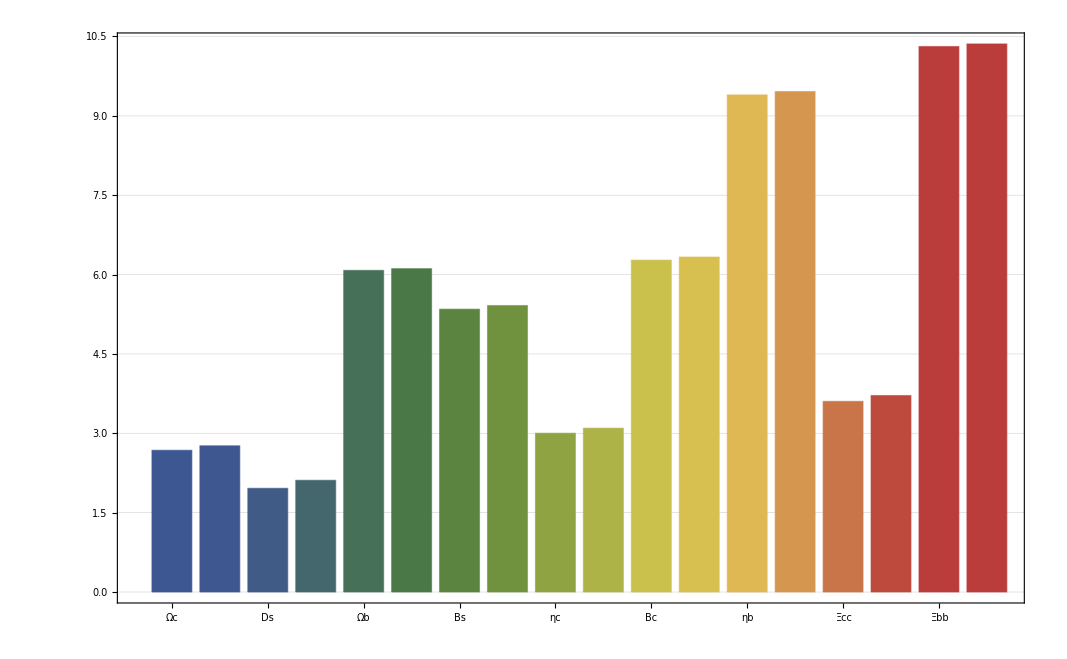

{My Error}

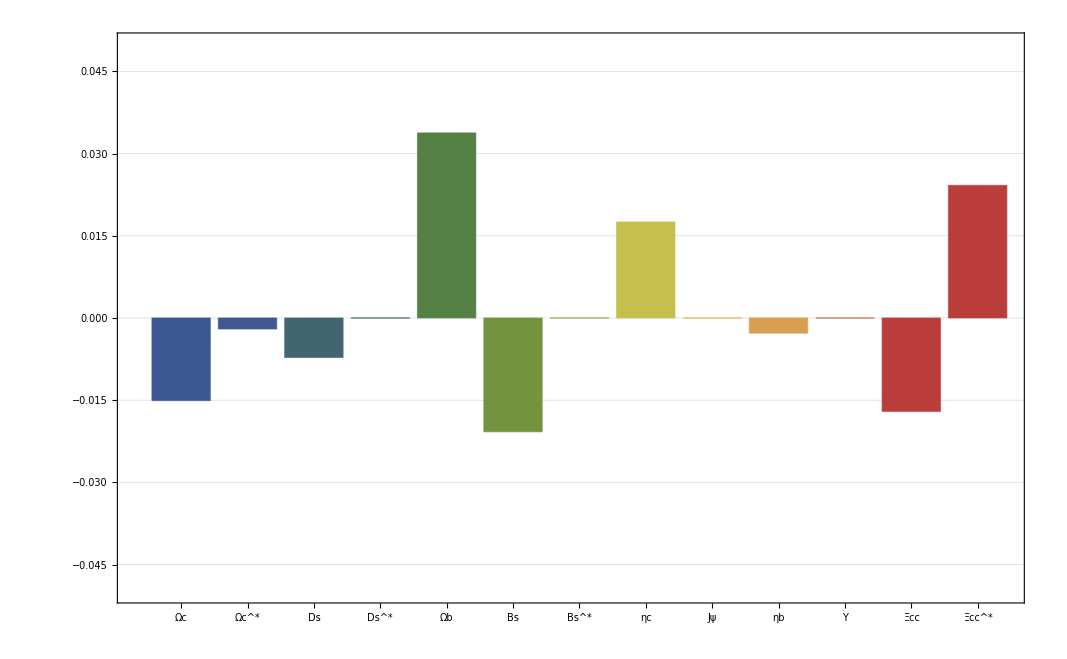

{Charge Radius}

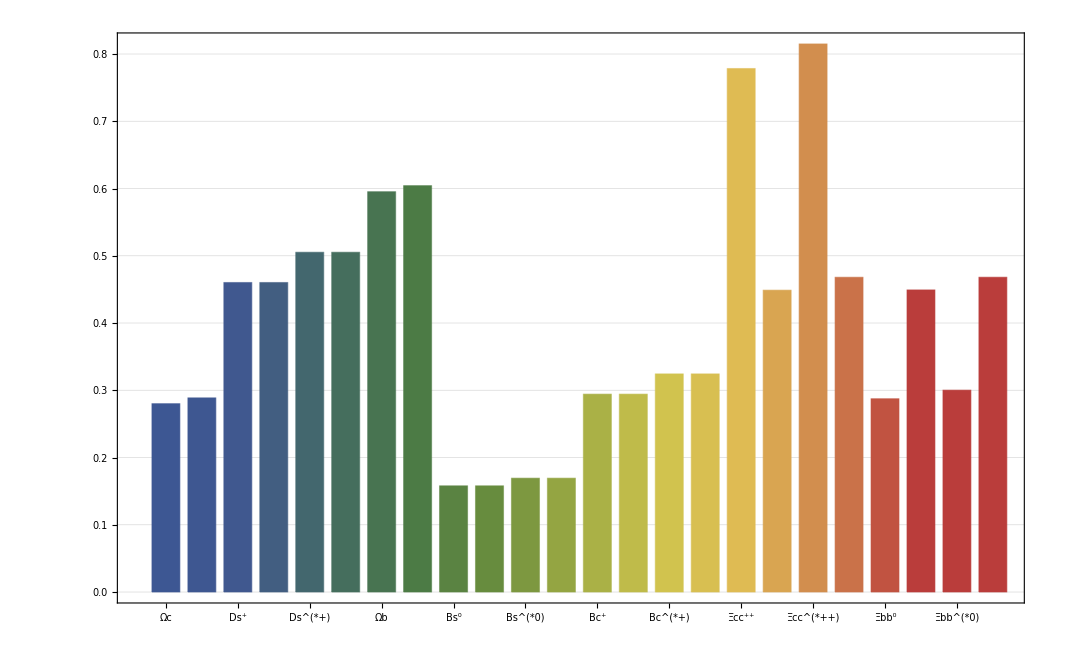

{Magnetic Moment}

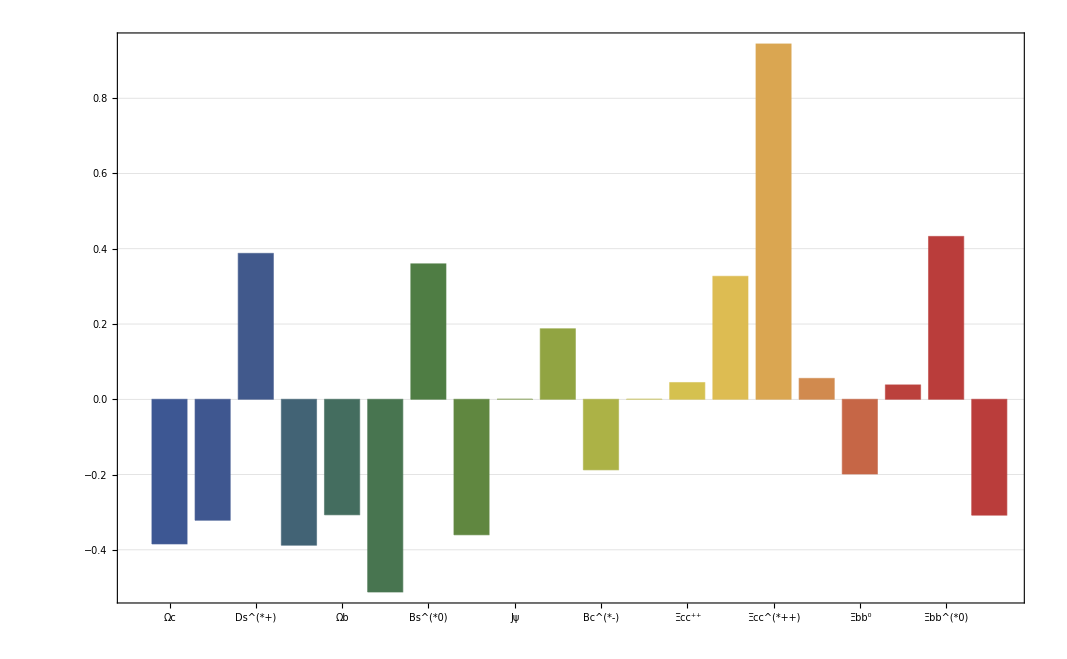

```mathematica
Get[NotebookDirectory[]<>"MITBagModel.wl"]

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
γμN=2.7928473446;

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.332)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωc 1/2+ 2.695"}
Ωc=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,32/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩc=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},Ωc];
μΩc=MagneticMoment[{0,-1/3,4/3,0,0},{0,0,0,0,0},Ωc];
{rΩc}
{{μΩc},{μΩc/μNp},γμN{μΩc/μNp}}

{"Ωc^* 3/2+ 2.766"}
ΩcStar=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩcStar=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
μΩcStar=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
{rΩcStar}
{{μΩcStar},{μΩcStar/μNp},γμN{μΩcStar/μNp}}

{"Ds 0- 1.968"}
Ds=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,16,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDsp=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},Ds];
rDsm=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},Ds];
{rDsp,rDsm}

{"Ds^* 1- 2.112"}
DsStar=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDspStar=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},DsStar];
rDsmStar=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},DsStar];
μDspStar=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},DsStar];
μDsmStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},DsStar];
{rDspStar,rDsmStar}
{{μDspStar,μDsmStar},{μDspStar/μNp,μDsmStar/μNp},γμN{μDspStar/μNp,μDsmStar/μNp}}

{"Ωb 1/2+ 6.046"}
Ωb=Hadron[{1,0,2,0},{{0,0,32/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩb=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},Ωb];
μΩb=MagneticMoment[{-1/3,0,4/3,0,0},{0,0,0,0,0},Ωb];
{rΩb}
{{μΩb},{μΩb/μNp},γμN{μΩb/μNp}}

{"Ωb^* 3/2+"}
ΩbStar=Hadron[{1,0,2,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩbStar=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
μΩbStar=MagneticMoment[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
{rΩbStar}
{{μΩbStar},{μΩbStar/μNp},γμN{μΩbStar/μNp}}

{"Bs 0- 5.367"}
Bs=Hadron[{1,0,1,0},{{0,0,16,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},Bs];
rBs0bar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},Bs];
{rBs0,rBs0bar}

{"Bs^* 1- 5.415"}
BsStar=Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0Star=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},BsStar];
rBs0barStar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},BsStar];
μBs0Star=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},BsStar];
μBs0barStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},BsStar];
{rBs0Star,rBs0barStar}
{{μBs0Star,μBs0barStar},{μBs0Star/μNp,μBs0barStar/μNp},γμN{μBs0Star/μNp,μBs0barStar/μNp}}

{"ηc 0- 2.984"}
ηc=Hadron[{0,2,0,0},{{0,0,0,0},{0,16,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rηc=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},ηc];
{rηc}

{"Jψ 1- 3.097"}
Jψ=Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rJψ=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},Jψ];
μJψ=MagneticMoment[{0,1,0,0,0},{0,1,0,0,0},Jψ];
{rJψ}
{{μJψ},{μJψ/μNp},γμN{μJψ/μNp}}

{"Bc 0- 6.275"}
Bc=Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcp=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},Bc];
rBcm=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},Bc];
{rBcp,rBcm}

{"Bc^* 1-"}
BcStar=Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcpStar=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},BcStar];
rBcmStar=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},BcStar];
μBcpStar=MagneticMoment[{0,1,0,0,0},{1,0,0,0,0},BcStar];
μBcmStar=MagneticMoment[{1,0,0,0,0},{0,1,0,0,0},BcStar];
{rBcpStar,rBcmStar}
{{μBcpStar,μBcmStar},{μBcpStar/μNp,μBcmStar/μNp},γμN{μBcpStar/μNp,μBcmStar/μNp}}

{"ηb 0- 9.399"}
ηb=Hadron[{2,0,0,0},{{16,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rηb=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},ηb];
{rηb}

{"Υ 1- 9.460"}
Υ=Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rΥ=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},Υ];
μΥ=MagneticMoment[{1,0,0,0,0},{1,0,0,0,0},Υ];
{rΥ}
{{μΥ},{μΥ/μNp},γμN{μΥ/μNp}}

{"Ξcc 1/2+ 3.621"}
Ξcc=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,32/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccpp=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},Ξcc];
rΞccp=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},Ξcc];
μΞccpp=MagneticMoment[{0,4/3,0,-1/3,0},{0,0,0,0,0},Ξcc];
μΞccp=MagneticMoment[{0,4/3,0,0,-1/3},{0,0,0,0,0},Ξcc];
{rΞccpp,rΞccp}
{{μΞccpp,μΞccp},{μΞccpp/μNp,μΞccp/μNp},γμN{μΞccpp/μNp,μΞccp/μNp}}

{"Ξcc^* 3/2+ 1.533"}
ΞccStar=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,-16/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccppStar=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
rΞccpStar=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
μΞccppStar=MagneticMoment[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
μΞccpStar=MagneticMoment[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
{rΞccppStar,rΞccpStar}
{{μΞccppStar,μΞccpStar},{μΞccppStar/μNp,μΞccpStar/μNp},γμN{μΞccppStar/μNp,μΞccpStar/μNp}}

{"Ξbb 1/2+"}
Ξbb=Hadron[{2,0,0,1},{{-8/3,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},Ξbb];
rΞbbm=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},Ξbb];
μΞbb0=MagneticMoment[{4/3,0,0,-1/3,0},{0,0,0,0,0},Ξbb];
μΞbbm=MagneticMoment[{4/3,0,0,0,-1/3},{0,0,0,0,0},Ξbb];
{rΞbb0,rΞbbm}
{{μΞbb0,μΞbbm},{μΞbb0/μNp,μΞbbm/μNp},γμN{μΞbb0/μNp,μΞbbm/μNp}}

{"Ξbb^* 3/2+"}
ΞbbStar=Hadron[{2,0,0,1},{{-8/3,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0Star=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
rΞbbmStar=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
μΞbb0Star=MagneticMoment[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
μΞbbmStar=MagneticMoment[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
{rΞbb0Star,rΞbbmStar}
{{μΞbb0Star,μΞbbmStar},{μΞbb0Star/μNp,μΞbbmStar/μNp},γμN{μΞbb0Star/μNp,μΞbbmStar/μNp}}


{"Mass Spectrum"}
BarChart[{First[Ωc],First[ΩcStar],First[Ds],First[DsStar],First[Ωb],First[ΩbStar],First[Bs],First[BsStar],First[ηc],First[Jψ],First[Bc],First[BcStar],First[ηb],First[Υ],First[Ξcc],First[ΞccStar],First[Ξbb],First[ΞbbStar]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Ωb^*","Bs","Bs^*","ηc","Jψ","Bc","Bc^*","ηb","Υ","Ξcc","Ξcc^*","Ξbb","Ξbb^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Ωc]-2.695),
(First[ΩcStar]-2.766),
(First[Ds]-1.968),
(First[DsStar]-2.112),
(First[Ωb]-6.046),
(First[Bs]-5.367),
(First[BsStar]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621),
(First[ΞccStar]-3.690)},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc","Ξcc^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩc,rΩcStar,rDsp,rDsm,rDspStar,rDsmStar,rΩb,rΩbStar,rBs0,rBs0bar,rBs0Star,rBs0barStar,rBcp,rBcm,rBcpStar,rBcmStar,rΞccpp,rΞccp,rΞccppStar,rΞccpStar,rΞbb0,rΞbbm,rΞbb0Star,rΞbbmStar},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^+","Ds^-","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^0","OverBar[Bs]^0","Bs^(*0)","OverBar[Bs]^(*0)","Bc^+","Bc^-","Bc^(*+)","Bc^(*-)","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩc/μNp,μΩcStar/μNp,μDspStar/μNp,μDsmStar/μNp,μΩb/μNp,μΩbStar/μNp,μBs0Star/μNp,μBs0barStar/μNp,μJψ/μNp,μBcpStar/μNp,μBcmStar/μNp,μΥ/μNp,μΞccpp/μNp,μΞccp/μNp,μΞccppStar/μNp,μΞccpStar/μNp,μΞbb0/μNp,μΞbbm/μNp,μΞbb0Star/μNp,μΞbbmStar/μNp},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^(*0)","OverBar[Bs]^(*0)","Jψ","Bc^(*+)","Bc^(*-)","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```